```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
n=12;L=100;
```

```mathematica
scores=ToAssociations[Import["scores.json"]]
```

<|12→<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},4,correct to i for disagreementCount greedy→{1.,96,0.}|>,0.02→1|>,6,0.3→1|>,1,25→1|>
 |  |  |  |

```mathematica
scores[["12"]]
```

<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},4,correct to i for disagreementCount greedy→{1.,0.505,0.2,0.095,90,0.,0.,0.,0.}|>,0.02→1|>,6,0.3→1|>
 |  |  |  |

```mathematica
listOfScores = Flatten[With[{nlist = PositionIndex[scores]},Table[With[{plist = PositionIndex[scores[[i]]]},Table[With[{qlist = PositionIndex[scores[[i,j]]]},Table[With[{mlist=PositionIndex[scores[[i,j,k]]]},Table[{nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]],scores[[nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]]]]},{l,1,Length[mlist]}]],{k,1,Length[qlist]}]],{j,1,Length[plist]}]],{i,1,Length[nlist]}]],3]
```

{{12,0.054,0.01,correct to i for edgeCountDistance greedy,{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},259,{25,3,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,70,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}
 |  |  |  |

```mathematica
PlotList=ToAssociations[Map[({#[[1]],#[[2]],#[[3]],#[[4]]}->ListPlot[#[[5]]])&,listOfScores]];
```

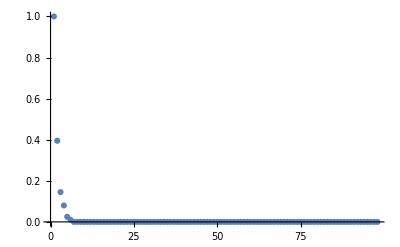

```mathematica
PlotList[{"12","0.1","0.01","correct to i for edgeCountDistance greedy"}]
```

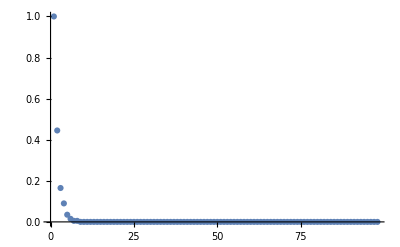

```mathematica
PlotList[{"12","0.1","0.01","correct to i for specDistance greedy"}]
```

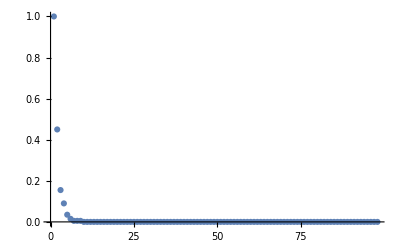

```mathematica
PlotList[{ToString[12],"0.1","0.01","correct to i for doublyStochasticMatrixDistance greedy"}]
```

```mathematica
metricList = {"edgeCountDistance","doublyStochasticMatrixDistance","specDistance","disagreementCount"};plist = {"0.05","0.1","0.2","0.3","0.4","0.5"};qlist = {"0.01", "0.05","0.1","0.2","0.3"};colors={Blue,Red,Green,Purple};
```

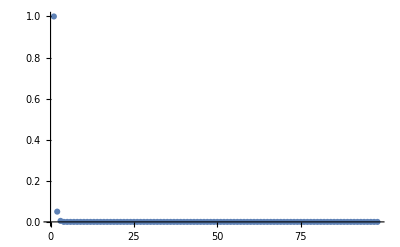

```mathematica
ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[1]], " greedy"]]]
```

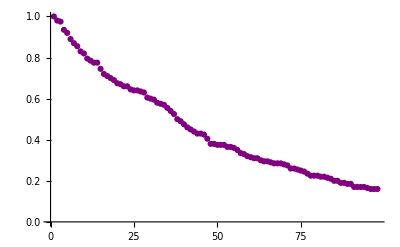

```mathematica
ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[4]], " greedy"]],PlotStyle->Purple]
```

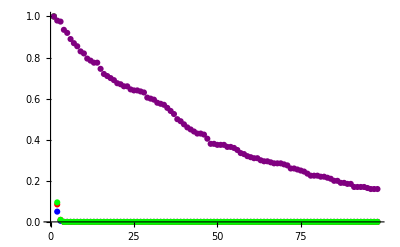

```mathematica
Show[Table[ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

```mathematica
FirstPlots = Table[Show[Table[ListPlot[scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]],{a,1,Length[plist]},{b,1,Length[qlist]}];
```

ListPlot::lpn: Missing[KeyAbsent,correct to i for doublyStochasticMatrixDistance greedy] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[Missing[KeyAbsent,correct to i for doublyStochasticMatrixDistance greedy],PlotStyle→color],,}].

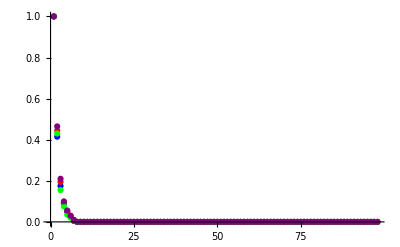
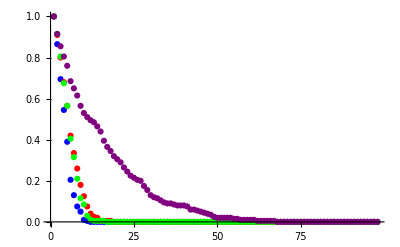
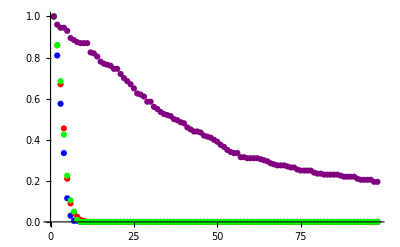
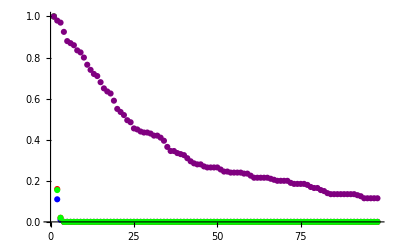
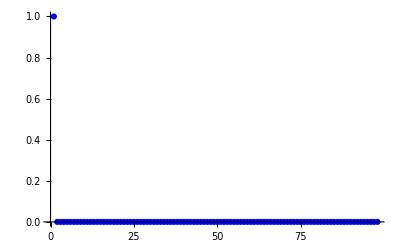
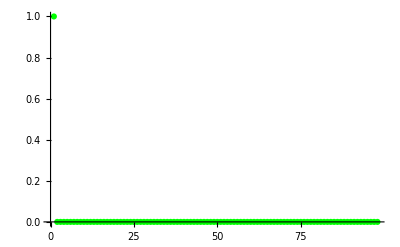
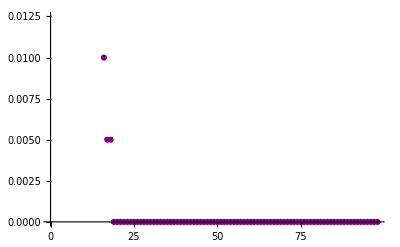
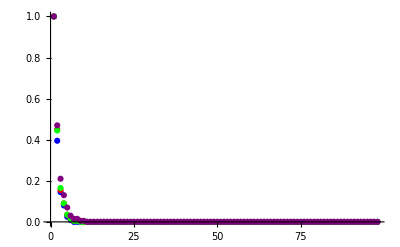
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | Show[{-Graphics-,ListPlot[Missing[KeyAbsent,correct to i for doublyStochasticMatrixDistance greedy],PlotStyle→RGBColor[1, 0, 0]],-Graphics-,-Graphics-}]
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)

```mathematica
FirstPlots//MatrixForm
```